## Derivatan av exponentialfunktionen a^x

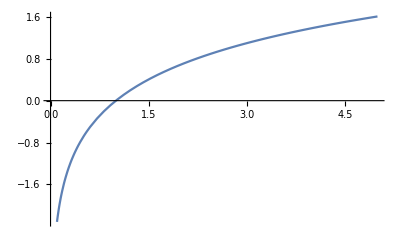

```mathematica
c[a_]:=Limit[(a^h-1)/h,h->0];
Plot[c[a],{a,0,5}]
```

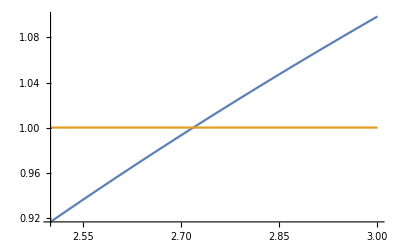

```mathematica
Plot[{c[a],1},{a,2.5,3}]
```

## e – Eulers tal

```mathematica
Solve[c[a]==1,a,Reals]
```

{{a→ⅇ}}

```mathematica
N[%,100]
```

{{a→2.718281828459045235360287471352662497757247093699959574966967627724076630353547594571382178525166427}}

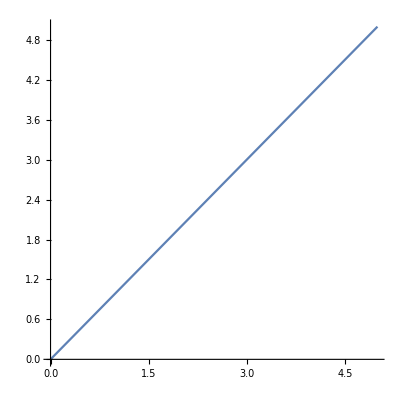

```mathematica
Plot[{c[ⅇ^b]},{b,0,5},AspectRatio->1]
```

```mathematica
Simplify[c[ⅇ^b],b∈Reals]
```